## Solution of the heat equation in 1D

```mathematica
^□
```

```mathematica
IP[f_,g_]:=Integrate[f g,{x,0,1}]
```

```mathematica
Subscript[k, n_]=n Pi
```

π n

```mathematica
Subscript[v, n_][x_]=Sin[Subscript[k, n] x]
```

sin(π n x)

#### Check orthogonality

```mathematica
J[m_,n_]=IP[Subscript[v, m][x],Subscript[v, n][x]]
```

(n sin(π m) cos(π n)-m cos(π m) sin(π n))/(π m^2-π n^2)

## A simple example

```mathematica
Subscript[U, 0][x_]=Subscript[v, 1][x]+1/3 Subscript[v, 4][x]
```

sin(π x)+1/3 sin(4 π x)

#### Find the coefficients

```mathematica
Subscript[B, n_]=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

((n^2+44) sin(π n))/(3 π (n^2-16) (n^2-1) (1/2-(sin(2 π n))/(4 π n)))

This is messy!

```mathematica
Subscript[B, n_]=Assuming[n∈Integers && n>0,IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]]
```

0

This misses the special cases!

```mathematica
Subscript[B, n_]:=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

```mathematica
Table[{n,Subscript[B, n]},{n,1,10}]
```

(1 | 1
2 | 0
3 | 0
4 | 1/3
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0)

#### Form M-th partial sum of the solution

```mathematica
uSum[M_,x_,t_]:=Sum[Subscript[B, n] Subscript[v, n][x]Exp[-Subscript[k, n]^2t],{n,1,M}]
```

```mathematica
u4[x_,t_]=uSum[4,x,t]
```

ⅇ^(-π^2 t) sin(π x)+1/3 ⅇ^(-16 π^2 t) sin(4 π x)

```mathematica
showU[t_]:=Plot[u4[x,t],{x,0,1},PlotRange->{-1.5,1.5}]
```

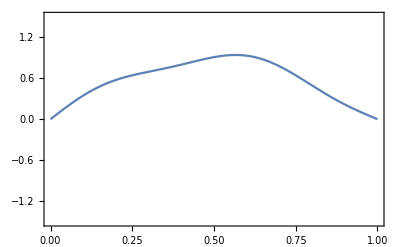

```mathematica
showU[0.01]
```

```mathematica
Manipulate[showU[10^p],{p,-4,0}]
```

```mathematica
Animate[showU[10^p],{p,-4,0},AnimationRunning->False]
```

## A not-so-simple example

```mathematica
Subscript[U, 0][x_]=Piecewise[{{2x,x<= 1/2},{2(1-x),x>1/2}}]
```

Piecewise[{{2 x, x≤1/2}, {2 (1-x), x>1/2}}]

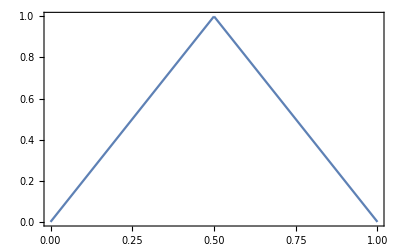

```mathematica
Plot[Subscript[U, 0][x],{x,0,1}]
```

#### Find the coefficients

```mathematica
Subscript[B, n_]=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

(2 (2 sin((π n)/2)-sin(π n)))/(π^2 n^2 (1/2-(sin(2 π n))/(4 π n)))

This is messy!

```mathematica
Subscript[B, n_]=Assuming[n∈Integers && n>0,IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]]
```

(8 sin((π n)/2))/(π^2 n^2)

This misses the special cases!

```mathematica
Subscript[B, n_]:=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

```mathematica
Table[{n,Subscript[B, n]},{n,1,10}]
```

(1 | 8/π^2
2 | 0
3 | -8/(9 π^2)
4 | 0
5 | 8/(25 π^2)
6 | 0
7 | -8/(49 π^2)
8 | 0
9 | 8/(81 π^2)
10 | 0)

#### Form M-th partial sum of the solution

```mathematica
uSum[M_,x_,t_]:=Sum[Subscript[B, n] Subscript[v, n][x]Exp[-Subscript[k, n]^2t],{n,1,M}]
```

```mathematica
u3[x_,t_]=uSum[3,x,t]
```

(8 ⅇ^(-π^2 t) sin(π x))/π^2-(8 ⅇ^(-9 π^2 t) sin(3 π x))/(9 π^2)

```mathematica
u5[x_,t_]=uSum[5,x,t]
```

(8 ⅇ^(-π^2 t) sin(π x))/π^2-(8 ⅇ^(-9 π^2 t) sin(3 π x))/(9 π^2)+(8 ⅇ^(-25 π^2 t) sin(5 π x))/(25 π^2)

```mathematica
u11[x_,t_]=uSum[11,x,t]
```

(8 ⅇ^(-π^2 t) sin(π x))/π^2-(8 ⅇ^(-9 π^2 t) sin(3 π x))/(9 π^2)+(8 ⅇ^(-25 π^2 t) sin(5 π x))/(25 π^2)-(8 ⅇ^(-49 π^2 t) sin(7 π x))/(49 π^2)+(8 ⅇ^(-81 π^2 t) sin(9 π x))/(81 π^2)-(8 ⅇ^(-121 π^2 t) sin(11 π x))/(121 π^2)

```mathematica
u21[x_,t_]=uSum[21,x,t];
```

```mathematica
u61[x_,t_]=uSum[61,x,t];
```

```mathematica
showU[t_]:=Plot[{u3[x,t],u5[x,t],u11[x,t],u21[x,t],u61[x,t]},{x,0,1},PlotRange->{0,1.1}]
```

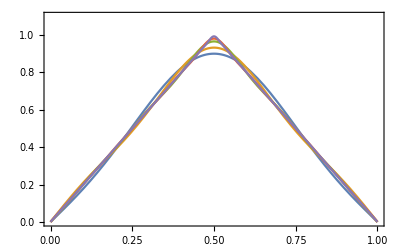

```mathematica
showU[0.0]
```

```mathematica
Manipulate[showU[10^p],{p,-4,0}]
```

```mathematica
Animate[showU[10^p],{p,-4,0},AnimationRunning->False]
```

```mathematica
Animate[showU[t],{t,0,1},AnimationRunning->False]
```